From the file ‘RefCurve_130143.txt.csv’.

```mathematica
t=Import["C:\\Users\\HILL\\Documents\\GitHub\\thesis\\figures\\oscillator\\guiding.csv"][[All,1]];
ch1=Import["C:\\Users\\HILL\\Documents\\GitHub\\thesis\\figures\\oscillator\\guiding.csv"][[All,2]];
ch2=Import["C:\\Users\\HILL\\Documents\\GitHub\\thesis\\figures\\oscillator\\guiding.csv"][[All,3]];
```

```mathematica
dT=0.04;thick=Directive[Thick];
```

```mathematica
ListLinePlot[
{Thread[{t,ch1}],
Thread[{t,ch2*6}]},
PlotStyle->{Automatic,Automatic},
PlotRange->All,ImageSize->Large,
Ticks->{{{-1*^-6,-1,dT,thick},{1*^-6,1,dT,thick},{2*^-6,2,dT,thick},{3*^-6,3,dT,thick},{4*^-6,4,dT,thick}},{{5,50,dT,thick},{10,100,dT,thick},{15,150,dT,thick}}},
TicksStyle->Directive["Label", 20,Black]]
```

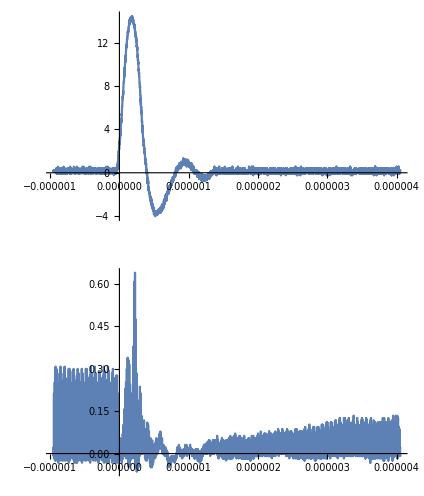

```mathematica
GraphicsColumn[{ListLinePlot[Thread[{t,ch1}],PlotRange->All],ListLinePlot[Thread[{t,ch2}],PlotRange->All]}]
```